```mathematica
ToMath[X_]:=ToExpression[StringReplace[X,{"[Log2]"-> "Log[2]","[Logme]"->"Log[me]","[LogD]"->"Log[D]","[Log1-x]"->"Log[1-x]"}]]
```

```mathematica
nn4=0.695911
nn5=-1.51716
nn6=-0.152045
nn7=4.36064
```

0.695911

-1.51716

-0.152045

4.36064

```mathematica
RR="ep^-1 * ( 1 - [Log2] + [Logme] )+ Pi^2 * (  - 1/6 )+ 331/30 - 6*[LogD] - 451/30*[Log2] +6*[Log2]*[LogD]+ 5*[Log2]^2 + 271/30*[Logme] -6*[Logme]*[LogD] - 4*[Logme]*[Log2] - [Logme]^2";
```

```mathematica
RRe=ToMath[RR]
```

331/30-π^2/6-(451 Log[2])/30+5 Log[2]^2-6 Log[D]+6 Log[2] Log[D]+(271 Log[me])/30-4 Log[2] Log[me]-6 Log[D] Log[me]-Log[me]^2+(1-Log[2]+Log[me])/ep

```mathematica
RR1="+ep^-1*(1/2)+361/60-3*[LogD]-3*[Log2]"
```

+ep^-1*(1/2)+361/60-3*[LogD]-3*[Log2]

```mathematica
"+ep^-1*(1/2)+361/60-3*[LogD]-3*[Log2]"
```

+ep^-1*(1/2)+361/60-3*[LogD]-3*[Log2]

```mathematica
RR1e=ToMath[RR1]
```

361/60+1/(2 ep)-3 Log[2]-3 Log[D]

```mathematica
RR1e+2/3ct//Expand
```

(2 ct)/3+RR1e

```mathematica
total="       + [Logme] * ( 46/15 - 2*[Log1-x] )+ Pi^2 * (  - 1/12 )+ 2809/360 - 1/8*nn7 + 1/8*nn6 + 9/8*nn5 -1/8*nn4 - 2*[Log1-x] - 167/30*[Log2] + 2*[Log2]*[Log1-x]";
```

```mathematica
tot=ToMath[total]
```

0.763912+Log[me] (46/15-2 Log[1-x])-2 Log[1-x]+2 Log[2] Log[1-x]

```mathematica
tot
```

0.763912+Log[me] (46/15-2 Log[1-x])-2 Log[1-x]+2 Log[2] Log[1-x]

```mathematica
totf=tot/.Log[1-x]->0
totL=Coefficient[tot,Log[1-x]]
```

0.763912+(46 Log[me])/15

-2+2 Log[2]-2 Log[me]

```mathematica
me=0.511/105.6
```

0.00483902

```mathematica
totf+6.1//N
totL//N
```

-9.48462

10.0484

```mathematica
a1=4 NIntegrate[x (1-x) Log[1+M^2/m^2 x (1-x)]/.M->m/.m->105,{x,0,1}];
a2=4 NIntegrate[x (1-x) Log[1+M^2/m^2 x (1-x)]/.M->105.6/.m->0.511,{x,0,1}];
VP=a1+a2
a1
```

6.1179

0.120859

```mathematica
VP=6.1179
totf/.me->0.510998928/105.6583715
totf+VP/.me->0.510998928/105.6583715
totL/.me->0.510998928/105.6583715
```

6.1179

-15.5846

-9.46672

10.0484

```mathematica
α/Pi totf/.me->0.510998928/105.6583715/.α->1/137.0359995698

totL /.me->0.510998928/105.6583715/.α->1/137.0359995698
```

-0.0362042

10.0495

```mathematica
0.9^0.1
```

0.989519

```mathematica
totE= α/Pi totf+(1-x)^(α/Pi*(totL))-1
totExp=(1-x)^(α/Pi*(totL))
```

-1+(1-x)^(3.1985 α)-4.96074 α

(1-x)^(3.1985 α)

```mathematica
me=0.511/105.6
α=1/137
```

0.00483902

1/137

```mathematica
NIntegrate[totE,{x,0,0.15/105}]
```

-0.0000517521

0.00142855

```mathematica
Table[{totE,α/Pi tot},{x,0.99,1,0.001}]
```

{{-0.138147,-0.143725},{-0.140354,-0.146185},{-0.142814,-0.148935},{-0.145595,-0.152053},{-0.148794,-0.155651},{-0.152563,-0.159908},{-0.157155,-0.165118},{-0.163039,-0.171834},{-0.171266,-0.1813},{-0.18515,-0.197483},{-1.03621,Indeterminate}}

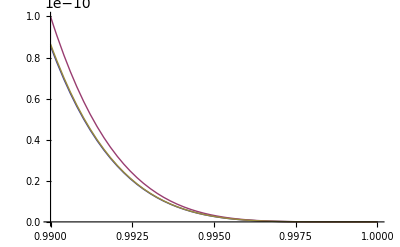

```mathematica
Plot[{(1-x)^5(1+α/Pi tot),(1-x)^5,(1-x)^5 totExp*(1+α/Pi totf)},{x,0.99,1}]
```

```mathematica
Series[d^a,{a,0,1}]
```

1+Log[d] a+O[a]^2

```mathematica
Log[0.511/105]
```

-5.32535

```mathematica
Plot[0.7639119392366363 +Log[0.511/105] (3.066666666666667 -2. Log[1. -1. x])-0.6137056388801094 Log[1. -1. x]]
```

```mathematica
Integrate[d^5 Log[d],{d,0,0.001}]/Integrate[d^5 ,{d,0,0.001}]//N
```

-7.07442

```mathematica
Integrate[d^5 Log[d],{d,0,0.01}]/Integrate[d^5,{d,0,0.01}]//N
```

-4.77184

```mathematica
Log[0.511/105.658]
```

-5.33159

```mathematica
ii=
NIntegrate[{(1-x)^5 (1+α/Pi tot),(1-x)^5,(1-x)^5 totExp*(1+α/Pi totf),(1-x)^5 totExp,(1-x)^5(1+α/Pi totf)},{x,0.99,1}]
```

{1.42064×10^-13,1.66667×10^-13,1.43698×10^-13,1.49097×10^-13,1.60632×10^-13}

```mathematica
NumberForm[1-ii[[1]]/ii[[2]],2](*fix order*)
NumberForm[1-ii[[3]]/ii[[2]],2](*resum*)
NumberForm[1-ii[[4]]/ii[[2]],2](*only exp*)
NumberForm[1-ii[[5]]/ii[[2]],2](*only fi*)
```

0.15

0.14

0.11

0.036

```mathematica
ii =NIntegrate[{(1-x)^5 (1+α/Pi tot),(1-x)^5,(1-x)^5 totExp*(1+α/Pi totf),(1-x)^5 totExp,(1-x)^5 (1+α/Pi totf)},{x,1-0.1/105,1}]
```

{9.91828×10^-20,1.24369×10^-19,1.01502×10^-19,1.05315×10^-19,1.19866×10^-19}

```mathematica
NumberForm[1-ii[[1]]/ii[[2]],2](*fix order*)
NumberForm[1-ii[[3]]/ii[[2]],2](*resum*)
NumberForm[1-ii[[4]]/ii[[2]],2](*only exp*)
NumberForm[1-ii[[5]]/ii[[2]],2]
```

0.2

0.18

0.15

0.036

```mathematica
totE
```

-1.03621+(1-x)^0.0233467

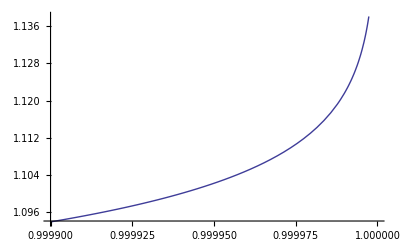

```mathematica
Plot[{α/Pi  tot/totE},{x,1-10^-4,1}]
```

```mathematica
totL
```

10.0484

```mathematica
totE
```

-1.03621+(1-x)^0.0233467

```mathematica
B550r=0.061
B550ho=-1.9*10^-5
dH=totf+VP
totL
Zal=13/137
α
```

0.061

-0.000019

-15.5846+VP

10.0484

13/137

α

```mathematica
exp=NIntegrate[(B550r(Pi Zal)^5(x^((α/Pi)totL)+α/Pi dH)+B550ho)x^5,{x,0,0.15/105.6}]
nocor=NIntegrate[(B550r (Pi Zal)^5 (1)+B550ho)x^5,{x,0,0.15/105.6}]
log=NIntegrate[(B550r (Pi Zal)^5 (1+(α/Pi) totL Log[x]+α/Pi dH)+B550ho)x^5,{x,0,0.15/105.6}]
```

1.37714×10^-22

1.70599×10^-22

1.35412×10^-22

```mathematica
1-exp/nocor
wp=1-log/nocor

wpp=1-exp/log
```

0.192762

0.206253

-0.0169967

```mathematica
wpp/wp
```

-0.082407

```mathematica
exp=NIntegrate[(B550r (Pi Zal)^5 (x^((α/Pi) totL)+α/Pi dH)+B550ho) x^5,{x,0,1/105.6}]
nocor=NIntegrate[(B550r (Pi Zal)^5 (1)+B550ho) x^5,{x,0,1/105.6}]
log=NIntegrate[(B550r (Pi Zal)^5 (1+(α/Pi) totL Log[x]+α/Pi dH)+B550ho) x^5,{x,0,1/105.6}]
```

1.27582×10^-17

1.49771×10^-17

1.26525×10^-17

```mathematica
1-exp/nocor
wp=1-log/nocor

wpp=1-exp/log
```

0.148151

0.155208

-0.00835323

```mathematica
wpp/wp
```

-0.0538195

```mathematica
exp/nocor
nocor/exp
```

0.851849

1.17392

```mathematica
nocor/exp
```

```mathematica
1/1.173917540569082
```

0.851849